```mathematica
A11={{1,1,0,0},{0,-1,1,0},{0,0,-1,1}};
A12=Table[{0,0,0,0},3];
A13=Table[{0,0},3];
A33={{0,1},{0,0},{1,0}};
A41={{0,0,0,1}};
A42={{0,0,0,0}};
A43={{0,0}};
X[x_]:={{0,Rb[x][[1]],Rc[x][[1]],Rc[x][[1]]}}/1000
Y[x_]:={{0,Rb[x][[2]],0,0}}/1000
A1=Flatten[{A11ᵀ,A12ᵀ,A13ᵀ},1]ᵀ;
A2=Flatten[{A12ᵀ,A11ᵀ,A13ᵀ},1]ᵀ;
XX[x_]:={X[x][[1]],X[x][[1]],X[x][[1]]}
YY[x_]:={Y[x][[1]],Y[x][[1]],Y[x][[1]]}
A31[x_]:=-A11*YY[x];
A32[x_]:=A11*XX[x];
A3[x_]:=Flatten[{A31[x]ᵀ,A32[x]ᵀ,A33ᵀ},1]ᵀ;
A4:=Flatten[{A41ᵀ,A42ᵀ,A43ᵀ},1]ᵀ;
A[x_]:=Flatten[{A1,A2,A3[x],A4},1]
```

```mathematica
A[x]//TableForm
```

1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0
0 | -0.09375 Sin[x] | 0 | 0 | 0 | 0.09375 Cos[x] | 0 | 0 | 0 | 1
0 | 0.09375 Sin[x] | 0 | 0 | 0 | -0.09375 Cos[x] | (93.75 Cos[x]+421.875 √(1-0.0493827 Sin[x]^2))/1000 | 0 | 0 | 0
0 | 0. | 0 | 0 | 0 | 0. | (-93.75 Cos[x]-421.875 √(1-0.0493827 Sin[x]^2))/1000 | (93.75 Cos[x]+421.875 √(1-0.0493827 Sin[x]^2))/1000 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
Dimensions@A[x]
```

{10,10}

```mathematica
aS1[x_]:={0,0}
aS2[x_]:=(as2[x] w1[x]^2+Vs2[x]*ϵ[x])/1000
aS3[x_]:=(as3[x] w1[x]^2+Vs3[x]*ϵ[x])/1000
wq2[x_]:=D[phi2[y],{y,1}]/.y->x
ϵq2[x_]:=D[phi2[y],{y,2}]/.y->x
ϵ2[x_]:=ϵq2[x] w1[x]^2+wq2[x]ϵ[x]
F1[x_]:=F1[x]={0,0}
F2[x_]:=-m2 aS2[x]
F3[x_]:=-m3 aS3[x]
G1=0;
G2=-m2 g;
G3=-m3 g;
MF1[x_]:=-(JprI) ϵ[x]
MF2[x_]:=-Jpr2 [x]ϵ2[x]
MF3[x_]:=MF3[x]=0
B[x_]:=-{
F1[x][[1]],
F2[x][[1]],
F3[x][[1]]+Fc[x],
F1[x][[2]]+G1,
F2[x][[2]]+G2,
F3[x][[2]]+G3,
MF1[x],
MF2[x]-F2[x][[1]]Rs2[x][[2]]/1000+(F2[x][[2]]+G2)Rs2[x][[1]]/1000,MF3[x]-F3[x][[1]]Rs3[x][[2]]/1000+(F3[x][[2]]+G3)Rs3[x][[1]]/1000,
0}
```

```mathematica
B[x]//Dimensions
```

{10}

```mathematica
xx=LinearSolve[A[x],B[x]];
```

```mathematica
xx/.x->Pi/3
```

{-1286.69,1286.69,1236.79,0.,274.866,-274.866,-226.127,-149.609,9.68431,79.1598}

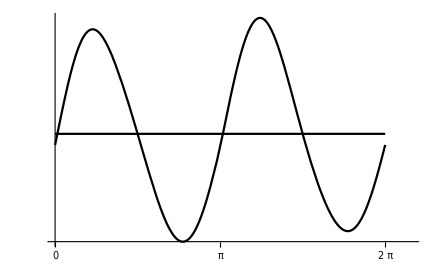

```mathematica
Plot[{Mprdv,xx[[10]]/.x->y},{y,0,2Pi},Ticks->{Table[i Pi/3,{i,0,12}],N@Table[1/10i,{i,0,10000}]},PlotStyle->Black,GridLines->{Table[i Pi/3,{i,0,6}],Table[i,{i,78.7,79.3,1/10}]},AxesStyle->{{Thick,Arrowheads[{0.04}]},{Thick,Arrowheads[{0.04}]}},PlotRange->{{0,2Pi+.5},Automatic}]
```

```mathematica
Table[xx[[10]]/.x->y,{y,Pi/4-1,Pi/2,0.1}]
```

{78.7319,78.7942,78.8631,78.9404,79.0164,79.0853,79.1429,79.1864,79.2142,79.2263,79.2234,79.2075,79.1807,79.1454,79.1036,79.0569,79.0067,78.9539}

```mathematica
(79.226-Mprdv)/Mprdv
```

0.00403637

```mathematica
xx=.
```

```mathematica
PolarPlot[{√((xx[[1]])^2+(xx[[5]])^2)/.x->y},{y,0,2Pi},PolarGridLines->Automatic,PolarAxes->True,PolarTicks->{"Degrees",{500,1000,1500,2000}},PlotStyle->Black,ImageSize->500]
```

-Graphics-

```mathematica
PolarPlot[{√((xx[[2]])^2+(xx[[6]])^2)/.x->y},{y,0,2Pi},PolarGridLines->Automatic,PolarAxes->True,PolarTicks->{"Degrees",{500,1000,1500,2000}},PlotStyle->Black,ImageSize->500]
```

-Graphics-

```mathematica
PolarPlot[{√((xx[[3]])^2+(xx[[7]])^2)/.x->y},{y,0,2Pi},PolarGridLines->Automatic,PolarAxes->True,PolarTicks->{"Degrees",{500,1000,1500,2000}},PlotStyle->Black,ImageSize->500]
```

-Graphics-

```mathematica
PolarPlot[{√((xx[[4]])^2+(xx[[8]])^2)/.x->y},{y,0,2Pi},PolarGridLines->Automatic,PolarAxes->True,PolarTicks->{"Degrees",{50,100,150,200,250}},PlotStyle->Black,ImageSize->500]
```

-Graphics-

```mathematica
PolarPlot[{√((xx[[1]])^2+(xx[[5]])^2)/.x->y},{y,0,2Pi},PolarGridLines->Automatic,PolarAxes->True,PolarTicks->{"Degrees",Automatic}]
```

```mathematica
xx/.x->Pi/4
```

{-1340.46,1340.46,1261.51,0.,243.539,-243.539,-182.893,-106.375,9.68431,79.2234}

```mathematica
Grid[{{Subscript[F, 10x],Subscript[F, 12x],Subscript[F, 23x],Subscript[F, 30x],Subscript[F, 10y],Subscript[F, 12y],Subscript[F, 23y],Subscript[F, 30y],Subscript[M, 30],Subscript[M, 1]},Map[Round[100#,3]/100&//N,xx/.x->Pi/6]},Frame->All,Spacings->{2, 2}]
```

F_(10 x) | F_(12 x) | F_(23 x) | F_(30 x) | F_(10 y) | F_(12 y) | F_(23 y) | F_(30 y) | M_30 | M_1
-1385.28 | 1385.28 | 1282.71 | 0. | 199.26 | -199.26 | -121.53 | -45.03 | 9.69 | 79.2

```mathematica
Grid[Flatten[{{{Subscript[F, 10x],Subscript[F, 12x],Subscript[F, 23x],Subscript[F, 30x],Subscript[F, 10y],Subscript[F, 12y],Subscript[F, 23y],Subscript[F, 30y],Subscript[M, 30],Subscript[M, 1]}},Table[□,10,10]},1],Frame->All,Spacings->{2, 2}]
```

F_(10 x) | F_(12 x) | F_(23 x) | F_(30 x) | F_(10 y) | F_(12 y) | F_(23 y) | F_(30 y) | M_30 | M_1
□ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □
□ | □ | □ | □ | □ | □ | □ | □ | □ | □

```mathematica
Grid[Flatten[{{{Subscript[F, 10x],Subscript[F, 12x],Subscript[F, 10y],Subscript[F, 12y],Subscript[M, 1]}},Table[□,3,5]},1],Frame->All,Spacings->{2, 2}]
```

F_(10 x) | F_(12 x) | F_(10 y) | F_(12 y) | M_1
□ | □ | □ | □ | □
□ | □ | □ | □ | □
□ | □ | □ | □ | □

```mathematica
Grid[Flatten[{{{Subscript[F, 12x],Subscript[F, 23x],Subscript[F, 12y],Subscript[F, 23y]}},Table[□,3,4]},1],Frame->All,Spacings->{2, 2}]
```

F_(12 x) | F_(23 x) | F_(12 y) | F_(23 y)
□ | □ | □ | □
□ | □ | □ | □
□ | □ | □ | □

```mathematica
Grid[Flatten[{{{Subscript[F, 23x],Subscript[F, 30x],Subscript[F, 23y],Subscript[F, 30y],Subscript[M, 30]}},Table[□,3,5]},1],Frame->All,Spacings->{2, 2}]
```

F_(23 x) | F_(30 x) | F_(23 y) | F_(30 y) | M_30
□ | □ | □ | □ | □
□ | □ | □ | □ | □
□ | □ | □ | □ | □

```mathematica
Table[√((xx[[4]])^2+(xx[[8]])^2)/.x->i,{i,0,2Pi,0.01}]//MatrixForm
```

(112.756
109.567
106.376
103.186
99.9956
96.8059
93.6173
90.4302
87.2452
84.0627
80.8832
77.7071
74.5349
71.3671
68.2041
65.0464
61.8944
58.7487
55.6097
52.4777
49.3534
46.2371
43.1292
40.0303
36.9408
33.861
30.7916
27.7328
24.6851
21.649
18.6248
15.613
12.6141
9.62833
6.65622
3.69814
0.754504
2.1743
5.08789
7.98586
10.8678
13.7334
16.5823
19.414
22.2283
25.0247
27.803
30.5627
33.3035
36.0251
38.7272
41.4094
44.0714
46.7129
49.3336
51.9331
54.5113
57.0677
59.6021
62.1143
64.6039
67.0707
69.5144
71.9347
74.3315
76.7044
79.0533
81.3778
83.6778
85.9531
88.2033
90.4284
92.6281
94.8023
96.9506
99.073
101.169
103.239
105.283
107.299
109.289
111.252
113.188
115.097
116.978
118.831
120.658
122.456
124.226
125.968
127.683
129.369
131.026
132.656
134.257
135.829
137.372
138.887
140.373
141.831
143.259
144.658
146.029
147.37
148.682
149.965
151.219
152.444
153.639
154.805
155.942
157.049
158.127
159.176
160.196
161.186
162.146
163.078
163.98
164.853
165.696
166.51
167.295
168.05
168.776
169.473
170.141
170.779
171.389
171.969
172.52
173.042
173.535
173.999
174.434
174.841
175.218
175.567
175.887
176.178
176.44
176.674
176.88
177.057
177.205
177.325
177.417
177.481
177.516
177.524
177.503
177.455
177.379
177.274
177.143
176.983
176.796
176.582
176.34
176.07
175.774
175.45
175.1
174.722
174.317
173.886
173.428
172.943
172.432
171.895
171.331
170.741
170.124
169.482
168.814
168.12
167.4
166.655
165.884
165.088
164.266
163.42
162.548
161.652
160.73
159.784
158.813
157.818
156.799
155.755
154.687
153.595
152.479
151.34
150.177
148.991
147.781
146.548
145.292
144.014
142.712
141.388
140.041
138.672
137.281
135.867
134.432
132.975
131.497
129.997
128.476
126.933
125.37
123.786
122.181
120.555
118.91
117.244
115.558
113.852
112.127
110.382
108.618
106.834
105.032
103.211
101.371
99.5126
97.6361
95.7414
93.8288
91.8984
89.9505
87.9852
86.0028
84.0033
81.9871
79.9542
77.9049
75.8393
73.7577
71.6603
69.5471
67.4186
65.2747
63.1158
60.942
58.7535
56.5506
54.3334
52.1021
49.8569
47.5981
45.3258
43.0403
40.7417
38.4303
36.1062
33.7697
31.421
29.0603
26.6878
24.3037
21.9082
19.5015
17.0839
14.6555
12.2166
9.76738
7.30805
4.83884
2.35995
0.128394
2.62598
5.1326
7.64803
10.1721
12.7045
15.245
17.7935
20.3497
22.9135
25.4845
28.0625
30.6475
33.239
35.837
38.4411
41.0512
43.6671
46.2885
48.9152
51.5469
54.1836
56.8249
59.4706
62.1205
64.7743
67.432
70.0931
72.7576
75.4252
78.0956
80.7687
83.4442
86.122
88.8017
91.4831
94.1661
96.8504
99.5358
102.222
104.909
107.596
110.284
108.052
104.889
101.726
98.5641
95.403
92.2433
89.0852
85.929
82.7749
79.6233
76.4744
73.3286
70.1861
67.0472
63.9121
60.7813
57.6549
54.5332
51.4166
48.3053
45.1996
42.0998
39.0062
35.9191
32.8388
29.7655
26.6996
23.6413
20.591
17.5489
14.5154
11.4907
8.4751
5.46894
2.47251
0.513912
3.49001
6.45549
9.41006
12.3534
15.2852
18.2052
21.1131
24.0085
26.8912
29.7609
32.6172
35.4599
38.2886
41.1031
43.903
46.688
49.4578
52.2121
54.9507
57.6731
60.3791
63.0683
65.7405
68.3954
71.0326
73.6518
76.2527
78.835
81.3985
83.9427
86.4674
88.9722
91.4569
93.9212
96.3647
98.7871
101.188
103.567
105.925
108.26
110.572
112.862
115.128
117.371
119.59
121.785
123.956
126.102
128.223
130.318
132.388
134.432
136.45
138.442
140.407
142.345
144.256
146.139
147.994
149.821
151.62
153.391
155.132
156.845
158.528
160.181
161.805
163.398
164.962
166.494
167.996
169.467
170.907
172.315
173.691
175.036
176.349
177.629
178.877
180.092
181.275
182.424
183.541
184.624
185.673
186.689
187.671
188.62
189.534
190.414
191.26
192.071
192.848
193.591
194.298
194.971
195.609
196.212
196.78
197.313
197.811
198.273
198.7
199.093
199.449
199.771
200.057
200.308
200.523
200.704
200.849
200.958
201.033
201.072
201.076
201.045
200.979
200.878
200.742
200.571
200.365
200.125
199.85
199.541
199.198
198.82
198.408
197.962
197.483
196.97
196.423
195.843
195.229
194.583
193.904
193.192
192.448
191.671
190.862
190.022
189.15
188.246
187.311
186.345
185.348
184.321
183.263
182.175
181.058
179.91
178.734
177.528
176.294
175.031
173.739
172.42
171.073
169.698
168.297
166.868
165.412
163.931
162.423
160.889
159.33
157.746
156.137
154.503
152.845
151.163
149.457
147.728
145.975
144.2
142.403
140.583
138.741
136.878
134.993
133.087
131.161
129.214
127.247
125.261
123.255
121.229
119.185
117.123
115.042
112.943
110.826
108.692
106.541
104.373
102.188
99.9878
97.7711
95.5389
93.2913
91.0286
88.7511
86.4591
84.1529
81.8327
79.4989
77.1516
74.7912
72.418
70.0321
67.634
65.2237
62.8017
60.368
57.9232
55.4672
53.0005
50.5233
48.0357
45.5382
43.0308
40.5139
37.9877
35.4524
32.9083
30.3556
27.7945
25.2252
22.6481
20.0632
17.4709
14.8713
12.2647
9.65124
7.03121
4.40478
1.77217
0.866422
3.51078
6.1607
8.81599
11.4765
14.1419
16.8121
19.4869
22.166
24.8494
27.5368
30.228
32.9228
35.6211
38.3227
41.0274
43.735
46.4453
49.1583
51.8736
54.5911
57.3108
60.0323
62.7555
65.4803
68.2065
70.9339
73.6624
76.3918
79.122
81.8528
84.584
87.3156
90.0472
92.7789
95.5103
98.2415
100.972
103.702
106.432
109.16
111.887)